```mathematica
eq1=m2*(xx''[t]+x''[t])+gamma0*Sqrt[Abs[xx'[t]]]+k*(xx[t]-xx0)==0
```

10000 √Abs[xx'[t]]+80000 (0.29804+xx[t])+2433 (x''[t]+xx''[t])==0

```mathematica
eq2=(m1+mm)*x''[t]+gamma1*x'[t]-k*(xx[t]-xx0)+Pi*rou*g*r*r*(x[t]-x0)-f*Cos[omega*t]-gamma0*Sqrt[Abs[xx'[t]]]==0
```

-10000 √Abs[xx'[t]]-6250 Cos[1.4005 t]+31557.3 (2+x[t])-80000 (0.29804+xx[t])+656.362 x'[t]+6201.54 x''[t]==0

```mathematica
(*DSolve[{eq1,eq2,x[0]==0,x'[0]==0,xx[0]==l0,xx'[0]==0},{x[t],xx[t]},t]*)
```

```mathematica
m1=4866
m2=2433
mm=1335.535
k=80000
g=9.8
rou=1025
r=1
l0=0.5
h2=0.8
f=6250
omega=1.4005
gamma0=10000
gamma1=656.3616
x0=-2
xx0=-0.29804
```

4866

2433

1335.54

80000

9.8

1025

1

0.5

0.8

6250

1.4005

10000

656.362

-2

-0.29804

```mathematica
sol=NDSolve[{eq1,eq2,x[0]==x0,x'[0]==0,xx[0]==xx0,xx'[0]==0},{x[t],xx[t]},{t,0,100}]
```

{{x[t]→InterpolatingFunction[…][t],xx[t]→InterpolatingFunction[…][t]}}

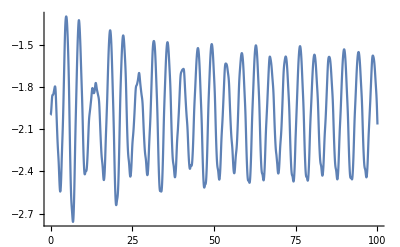

```mathematica
Plot[x[t]/.sol,{t,0,100}]
```

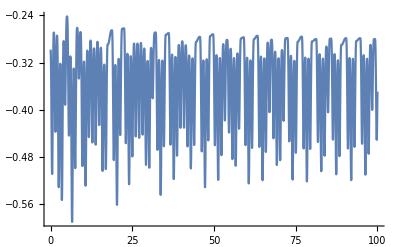

```mathematica
Plot[xx[t]/.sol,{t,0,100}]
```

```mathematica
q[t_]=sol[[1,2]][[2]]
```

InterpolatingFunction[…][t]

```mathematica
q'[t]
```

InterpolatingFunction[…][t]

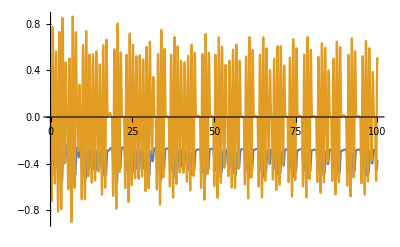

```mathematica
Plot[{q[t],q'[t]},{t,0,100}]
```

```mathematica
p=NIntegrate[q'[t]^2,{t,60,100}]/60
```

0.000503437

```mathematica
(*0.00047836678240043354*)
```